```mathematica
MyShow[m_,g_]:=TableForm[{Graph[g,GraphLayout->"TutteEmbedding",ImageSize->150, VertexLabels->"Name"],
Graph[g,GraphLayout->"CircularEmbedding",ImageSize->150, VertexLabels->"Name"],Labeled[TraditionalForm[m],Style[TraditionalForm[FullSimplify[m[[1,1]]+m[[1,2]]]],Red,Bold]]},TableDirections->Row]
```

```mathematica
MyShow2[m_,g_]:=Labeled[TableForm[m,TableHeadings->{ edges,None}],Style[TraditionalForm[FullSimplify[m[[1,1]]+m[[1,2]]]],Red,Bold]]
```

```mathematica
ContractGraph[g_,e_]:=Graph[VertexContract[gempty,{e[[1]],e[[2]]}],VertexLabels->{e[[1]]->{e}}]
```

```mathematica
gempty:=CycleGraph[5]
```

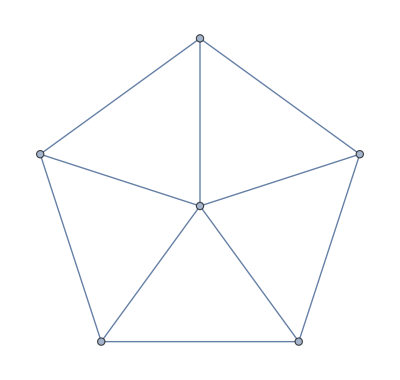

```mathematica
WheelGraph[6]
```

```mathematica
EdgeList[WheelGraph[6]]
```

{1<->2,1<->3,1<->4,1<->5,1<->6,2<->3,2<->6,3<->4,4<->5,5<->6}

```mathematica
edges=Sort[DeleteDuplicates[Join[EdgeList[CompleteGraph[5]],{1<->6,2<->6,3<->6,4<->6,5<->6}]]]
```

{1<->2,1<->3,1<->4,1<->5,1<->6,2<->3,2<->4,2<->5,2<->6,3<->4,3<->5,3<->6,4<->5,4<->6,5<->6}

```mathematica
empty:=Table[With[{s=Symbol["α"<>ToString[e[[1]]]<>ToString[e[[2]]]]},{s,λ-s}],{e,edges}];MyShow2[empty,gempty]
```

1<->2 | α12 | -α12+λ
1<->3 | α13 | -α13+λ
1<->4 | α14 | -α14+λ
1<->5 | α15 | -α15+λ
1<->6 | α16 | -α16+λ
2<->3 | α23 | -α23+λ
2<->4 | α24 | -α24+λ
2<->5 | α25 | -α25+λ
2<->6 | α26 | -α26+λ
3<->4 | α34 | -α34+λ
3<->5 | α35 | -α35+λ
3<->6 | α36 | -α36+λ
4<->5 | α45 | -α45+λ
4<->6 | α46 | -α46+λ
5<->6 | α56 | -α56+λλ

```mathematica
Table[With[{s=Symbol["α"<>ToString[e[[1]]]<>ToString[e[[2]]]]},{s,λ-s}],{e,edges}]
```

{{α12,-α12+λ},{α13,-α13+λ},{α14,-α14+λ},{α15,-α15+λ},{α16,-α16+λ},{α23,-α23+λ},{α24,-α24+λ},{α25,-α25+λ},{α26,-α26+λ},{α34,-α34+λ},{α35,-α35+λ},{α45,-α45+λ},{α56,-α56+λ}}

```mathematica
alfa:={{α12,-α12+λ},{α13,-α13+λ},{α14,-α14+λ},{α15,-α15+λ},{α16,-α16+λ},{α23,-α23+λ},{α24,-α24+λ},{α25,-α25+λ},{α26,-α26+λ},{α34,-α34+λ},{α35,-α35+λ},{α45,-α45+λ},{α56,-α56+λ}};MyShow2[alfa,ContractGraph[gempty,1<->3]]
```

1<->3 | α | 0
1<->4 | 0 | α
2<->4 | γ2 | α-γ2
2<->5 | δ1 | α-δ1
3<->5 | 0 | αα

```mathematica
onethreecontract:=alfa;
```

```mathematica
onethree:=empty-alfa;MyShow2[onethree,EdgeAdd[gempty,1<->3]]
```

1<->3 | 0 | -α+λ
1<->4 | β | -α-β+λ
2<->4 | γ-γ2 | -α-γ+γ2+λ
2<->5 | δ-δ1 | -α-δ+δ1+λ
3<->5 | ϵ | -α-ϵ+λλ-α

```mathematica
beta:={{0,β},{β,0},{0,β},{δ2,β-δ2},{ϵ1,β-ϵ1}};MyShow2[beta,ContractGraph[gempty,1<->4]]
```

1<->3 | 0 | β
1<->4 | β | 0
2<->4 | 0 | β
2<->5 | δ2 | β-δ2
3<->5 | ϵ1 | β-ϵ1β

```mathematica
onefourcontract:=beta;
```

```mathematica
onefour:=empty-beta;MyShow2[onefour,EdgeAdd[gempty,1<->4]]
```

1<->3 | α | -α-β+λ
1<->4 | 0 | -β+λ
2<->4 | γ | -β-γ+λ
2<->5 | δ-δ2 | -β-δ+δ2+λ
3<->5 | ϵ-ϵ1 | -β-ϵ+ϵ1+λλ-β

```mathematica
gamma:={{α1,γ-α1},{0,γ},{γ,0},{0,γ},{ϵ2,γ-ϵ2}};MyShow2[gamma,ContractGraph[gempty,2<->4]]
```

1<->3 | α1 | -α1+γ
1<->4 | 0 | γ
2<->4 | γ | 0
2<->5 | 0 | γ
3<->5 | ϵ2 | γ-ϵ2γ

```mathematica
twofourcontract:=gamma;
```

```mathematica
twofour:=empty-gamma;MyShow2[twofour,EdgeAdd[gempty,2<->4]]
```

1<->3 | α-α1 | -α+α1-γ+λ
1<->4 | β | -β-γ+λ
2<->4 | 0 | -γ+λ
2<->5 | δ | -γ-δ+λ
3<->5 | ϵ-ϵ2 | -γ-ϵ+ϵ2+λλ-γ

```mathematica
delta:={{α2,δ-α2},{β1,δ-β1},{0,δ},{δ,0},{0,δ}};MyShow2[delta,ContractGraph[gempty,2<->5]]
```

1<->3 | α2 | -α2+δ
1<->4 | β1 | -β1+δ
2<->4 | 0 | δ
2<->5 | δ | 0
3<->5 | 0 | δδ

```mathematica
twofivecontract:=delta;
```

```mathematica
twofive:=empty-delta;MyShow2[twofive,EdgeAdd[gempty,2<->5]]
```

1<->3 | α-α2 | -α+α2-δ+λ
1<->4 | β-β1 | -β+β1-δ+λ
2<->4 | γ | -γ-δ+λ
2<->5 | 0 | -δ+λ
3<->5 | ϵ | -δ-ϵ+λλ-δ

```mathematica
epsilon:={{0,ϵ},{β2,ϵ-β2},{γ1,ϵ-γ1},{0,ϵ},{ϵ,0}};MyShow2[epsilon,ContractGraph[gempty,3<->5]]
```

1<->3 | 0 | ϵ
1<->4 | β2 | -β2+ϵ
2<->4 | γ1 | -γ1+ϵ
2<->5 | 0 | ϵ
3<->5 | ϵ | 0ϵ

```mathematica
threefive:=empty-epsilon;MyShow2[threefive,EdgeAdd[gempty,3<->5]]
```

1<->3 | α | -α-ϵ+λ
1<->4 | β-β2 | -β+β2-ϵ+λ
2<->4 | γ-γ1 | -γ+γ1-ϵ+λ
2<->5 | δ | -δ-ϵ+λ
3<->5 | 0 | -ϵ+λλ-ϵ

```mathematica
threefivecontract:=epsilon;
```

```mathematica
oneamigo1:=onethree-onefourcontract;MyShow2[oneamigo1,EdgeAdd[gempty,{1<->3,1<->4}]]
```

1<->3 | 0 | -α-β+λ
1<->4 | 0 | -α-β+λ
2<->4 | γ-γ2 | -α-β-γ+γ2+λ
2<->5 | δ-δ1-δ2 | -α-β-δ+δ1+δ2+λ
3<->5 | ϵ-ϵ1 | -α-β-ϵ+ϵ1+λ-α-β+λ

```mathematica
oneamigo2:=twofive-twofourcontract;MyShow2[oneamigo2,EdgeAdd[gempty,{2<->5,2<->4}]]
```

1<->3 | α-α1-α2 | -α+α1+α2-γ-δ+λ
1<->4 | β-β1 | -β+β1-γ-δ+λ
2<->4 | 0 | -γ-δ+λ
2<->5 | 0 | -γ-δ+λ
3<->5 | ϵ-ϵ2 | -γ-δ-ϵ+ϵ2+λ-γ-δ+λ

```mathematica
oneamigo3:=threefive;
```

```mathematica
twoamigo1:=twofive-twofourcontract;MyShow2[twoamigo1,EdgeAdd[gempty,{2<->5,2<->4}]]
```

1<->3 | α-α1-α2 | -α+α1+α2-γ-δ+λ
1<->4 | β-β1 | -β+β1-γ-δ+λ
2<->4 | 0 | -γ-δ+λ
2<->5 | 0 | -γ-δ+λ
3<->5 | ϵ-ϵ2 | -γ-δ-ϵ+ϵ2+λ-γ-δ+λ

```mathematica
twoamigo2:=onethree-threefivecontract;MyShow2[twoamigo2,EdgeAdd[gempty,{3<->5,3<->1}]]
```

1<->3 | 0 | -α-ϵ+λ
1<->4 | β-β2 | -α-β+β2-ϵ+λ
2<->4 | γ-γ1-γ2 | -α-γ+γ1+γ2-ϵ+λ
2<->5 | δ-δ1 | -α-δ+δ1-ϵ+λ
3<->5 | 0 | -α-ϵ+λ-α+λ-ϵ

```mathematica
twoamigo3:=onefour;
```

```mathematica
threeamigo1:=onethree-threefivecontract;MyShow2[threeamigo1,EdgeAdd[gempty,{3<->5,3<->1}]]
```

1<->3 | 0 | -α-ϵ+λ
1<->4 | β-β2 | -α-β+β2-ϵ+λ
2<->4 | γ-γ1-γ2 | -α-γ+γ1+γ2-ϵ+λ
2<->5 | δ-δ1 | -α-δ+δ1-ϵ+λ
3<->5 | 0 | -α-ϵ+λ-α+λ-ϵ

```mathematica
threeamigo2:=onefour-twofourcontract;MyShow2[threeamigo2,EdgeAdd[gempty,{4<->1,4<->2}]]
```

1<->3 | α-α1 | -α+α1-β-γ+λ
1<->4 | 0 | -β-γ+λ
2<->4 | 0 | -β-γ+λ
2<->5 | δ-δ2 | -β-γ-δ+δ2+λ
3<->5 | ϵ-ϵ1-ϵ2 | -β-γ-ϵ+ϵ1+ϵ2+λ-β-γ+λ

```mathematica
threeamigo3:=twofive;
```

```mathematica
fouramigo1:=onefour-twofourcontract;MyShow2[fouramigo1,EdgeAdd[gempty,{4<->1,4<->2}]]
```

1<->3 | α-α1 | -α+α1-β-γ+λ
1<->4 | 0 | -β-γ+λ
2<->4 | 0 | -β-γ+λ
2<->5 | δ-δ2 | -β-γ-δ+δ2+λ
3<->5 | ϵ-ϵ1-ϵ2 | -β-γ-ϵ+ϵ1+ϵ2+λ-β-γ+λ

```mathematica
fouramigo2:=twofive-threefivecontract;MyShow2[fouramigo2,EdgeAdd[gempty,{5<->2,5<->3}]]
```

1<->3 | α-α2 | -α+α2-δ-ϵ+λ
1<->4 | β-β1-β2 | -β+β1+β2-δ-ϵ+λ
2<->4 | γ-γ1 | -γ+γ1-δ-ϵ+λ
2<->5 | 0 | -δ-ϵ+λ
3<->5 | 0 | -δ-ϵ+λ-δ+λ-ϵ

```mathematica
fouramigo3:=onethree;
```

```mathematica
fiveamigo1:=twofive-threefivecontract;MyShow2[fiveamigo1,EdgeAdd[gempty,{5<->2,5<->3}]]
```

1<->3 | α-α2 | -α+α2-δ-ϵ+λ
1<->4 | β-β1-β2 | -β+β1+β2-δ-ϵ+λ
2<->4 | γ-γ1 | -γ+γ1-δ-ϵ+λ
2<->5 | 0 | -δ-ϵ+λ
3<->5 | 0 | -δ-ϵ+λ-δ+λ-ϵ

```mathematica
fiveamigo2:=onethree-onefourcontract;MyShow2[fiveamigo2,EdgeAdd[gempty,{1<->3,1<->4}]]
```

1<->3 | 0 | -α-β+λ
1<->4 | 0 | -α-β+λ
2<->4 | γ-γ2 | -α-β-γ+γ2+λ
2<->5 | δ-δ1-δ2 | -α-β-δ+δ1+δ2+λ
3<->5 | ϵ-ϵ1 | -α-β-ϵ+ϵ1+λ-α-β+λ

```mathematica
fiveamigo3:=twofour;
```

```mathematica
full:=2*empty-( oneamigo1+oneamigo2+oneamigo3)//FullSimplify;MyShow2[full,EdgeAdd[gempty,Table[i<->6,{i,5}]]]
```

1<->3 | α1+α2 | α-α1-α2+β+γ+δ+ϵ-λ
1<->4 | β1+β2 | α+β-β1-β2+γ+δ+ϵ-λ
2<->4 | γ1+γ2 | α+β+γ-γ1-γ2+δ+ϵ-λ
2<->5 | δ1+δ2 | α+β+γ+δ-δ1-δ2+ϵ-λ
3<->5 | ϵ1+ϵ2 | α+β+γ+δ+ϵ-ϵ1-ϵ2-λα+β+γ+δ-λ+ϵ

```mathematica
onegone:=full+oneamigo1//FullSimplify;MyShow2[onegone,EdgeAdd[gempty,Table[i<->6,{i,{2,3,4,5}}]]]
```

1<->3 | α1+α2 | -α1-α2+γ+δ+ϵ
1<->4 | β1+β2 | -β1-β2+γ+δ+ϵ
2<->4 | γ+γ1 | -γ1+δ+ϵ
2<->5 | δ | γ+ϵ
3<->5 | ϵ+ϵ2 | γ+δ-ϵ2γ+δ+ϵ

```mathematica
fivegone:=full+fiveamigo1//FullSimplify;MyShow2[fivegone,EdgeAdd[gempty,Table[i<->6,{i,{1,2,3,4}}]]]
```

1<->3 | α+α1 | -α1+β+γ
1<->4 | β | α+γ
2<->4 | γ+γ2 | α+β-γ2
2<->5 | δ1+δ2 | α+β+γ-δ1-δ2
3<->5 | ϵ1+ϵ2 | α+β+γ-ϵ1-ϵ2α+β+γ

```mathematica
twogone:=full+twoamigo1//FullSimplify;MyShow2[twogone,EdgeAdd[gempty,Table[i<->6,{i,{1,3,4,5}}]]]
```

1<->3 | α | β+ϵ
1<->4 | β+β2 | α-β2+ϵ
2<->4 | γ1+γ2 | α+β-γ1-γ2+ϵ
2<->5 | δ1+δ2 | α+β-δ1-δ2+ϵ
3<->5 | ϵ+ϵ1 | α+β-ϵ1α+β+ϵ

```mathematica
onefivegone:=full+fiveamigo1+oneamigo1//FullSimplify;MyShow2[onefivegone,EdgeAdd[gempty,Table[i<->6,{i,{2,3,4}}]]]
```

1<->3 | α+α1 | -α-α1+γ+λ
1<->4 | β | -β+γ+λ
2<->4 | 2 γ | -γ+λ
2<->5 | δ | γ-δ+λ
3<->5 | ϵ+ϵ2 | γ-ϵ-ϵ2+λγ+λ

```mathematica
onetwofivegone:=onefivegone+delta//FullSimplify;MyShow2[onetwofivegone,EdgeAdd[gempty,Table[i<->6,{i,{3,4}}]]]
```

1<->3 | α+α1+α2 | -α-α1-α2+γ+δ+λ
1<->4 | β+β1 | -β-β1+γ+δ+λ
2<->4 | 2 γ | -γ+δ+λ
2<->5 | 2 δ | γ-δ+λ
3<->5 | ϵ+ϵ2 | γ+δ-ϵ-ϵ2+λγ+δ+λ

```mathematica
onethreefivegone:=onefivegone+delta//FullSimplify;MyShow2[onetwofivegone,EdgeAdd[gempty,Table[i<->6,{i,{3,4}}]]]
```

1<->3 | α+α1+α2 | -α-α1-α2+γ+δ+λ
1<->4 | β+β1 | -β-β1+γ+δ+λ
2<->4 | 2 γ | -γ+δ+λ
2<->5 | 2 δ | γ-δ+λ
3<->5 | ϵ+ϵ2 | γ+δ-ϵ-ϵ2+λγ+δ+λ

```mathematica
withoutspike1:=full+oneamigo1//FullSimplify;MyShow2[withoutspike1,EdgeAdd[gempty,Table[i<->6,{i,2,5}]]]
```

1<->3 | α1+α2 | -α1-α2+γ+δ+ϵ
1<->4 | β1+β2 | -β1-β2+γ+δ+ϵ
2<->4 | γ+γ1 | -γ1+δ+ϵ
2<->5 | δ | γ+ϵ
3<->5 | ϵ+ϵ2 | γ+δ-ϵ2γ+δ+ϵ

```mathematica
withoutspike2:=full+oneamigo2//FullSimplify;MyShow2[withoutspike2,EdgeAdd[gempty,Table[i<->6,{i,{1,3,4,5}}]]]
```

1<->3 | α | β+ϵ
1<->4 | β+β2 | α-β2+ϵ
2<->4 | γ1+γ2 | α+β-γ1-γ2+ϵ
2<->5 | δ1+δ2 | α+β-δ1-δ2+ϵ
3<->5 | ϵ+ϵ1 | α+β-ϵ1α+β+ϵ

```mathematica
without2spikes1:=withoutspike1+oneamigo2//FullSimplify;MyShow2[without2spikes1,EdgeAdd[gempty,Table[i<->6,{i,{3,4,5}}]]]
```

1<->3 | α | -α+ϵ+λ
1<->4 | β+β2 | -β-β2+ϵ+λ
2<->4 | γ+γ1 | -γ-γ1+ϵ+λ
2<->5 | δ | -δ+ϵ+λ
3<->5 | 2 ϵ | -ϵ+λλ+ϵ

```mathematica
without3spikes1:=without2spikes1+empty//FullSimplify;MyShow2[without3spikes1,EdgeAdd[gempty,Table[i<->6,{i,{1,5}}]]]
```

1<->3 | 2 α | -2 α+ϵ+2 λ
1<->4 | 2 β+β2 | -2 β-β2+ϵ+2 λ
2<->4 | 2 γ+γ1 | -2 γ-γ1+ϵ+2 λ
2<->5 | 2 δ | -2 δ+ϵ+2 λ
3<->5 | 3 ϵ | -2 ϵ+2 λ2 λ+ϵ

```mathematica
without2spikes2:=withoutspike2+oneamigo1//FullSimplify;MyShow2[without2spikes2,EdgeAdd[gempty,Table[i<->6,{i,{3,4,5}}]]]
```

1<->3 | α | -α+ϵ+λ
1<->4 | β+β2 | -β-β2+ϵ+λ
2<->4 | γ+γ1 | -γ-γ1+ϵ+λ
2<->5 | δ | -δ+ϵ+λ
3<->5 | 2 ϵ | -ϵ+λλ+ϵ

```mathematica
without3spikes2:=without2spikes2+empty//FullSimplify;MyShow2[without3spikes2,EdgeAdd[gempty,Table[i<->6,{i,{1,5}}]]]
```

1<->3 | 2 α | -2 α+ϵ+2 λ
1<->4 | 2 β+β2 | -2 β-β2+ϵ+2 λ
2<->4 | 2 γ+γ1 | -2 γ-γ1+ϵ+2 λ
2<->5 | 2 δ | -2 δ+ϵ+2 λ
3<->5 | 3 ϵ | -2 ϵ+2 λ2 λ+ϵ

```mathematica
Assuming[
{α>0,β>0,γ>0,δ>0,ϵ>0,α1>=0,α2>=0,β1>=0,β2>=0,γ1>=0,γ2>=0,δ1>=0,δ2>=0,ϵ1>=0,ϵ>=0},
Solve[2*empty-( oneamigo1+oneamigo2+oneamigo3)=={{0,0},{0,0},{0,0},{0,0},{0,0}}]
]
```

{{α2→-α1,β2→-β1,γ2→-γ1,δ2→-δ1,ϵ2→-ϵ1,λ→α+β+γ+δ+ϵ}}

```mathematica
Clear[sols]
```

```mathematica
sols=Association[]
```

<||>

```mathematica
sols[1]=empty
```

{{α,-α+λ},{β,-β+λ},{γ,-γ+λ},{δ,-δ+λ},{ϵ,-ϵ+λ}}

```mathematica
sols[2]=alfa
```

{{α,0},{0,α},{γ2,α-γ2},{δ1,α-δ1},{0,α}}

```mathematica
sols[3]=sols[1]-sols[2]
```

{{0,-α+λ},{β,-α-β+λ},{γ-γ2,-α-γ+γ2+λ},{δ-δ1,-α-δ+δ1+λ},{ϵ,-α-ϵ+λ}}

```mathematica
sols[4]=beta
```

{{0,β},{β,0},{0,β},{δ2,β-δ2},{ϵ1,β-ϵ1}}

```mathematica
sols[5]=sols[1]-sols[4]
```

{{α,-α-β+λ},{0,-β+λ},{γ,-β-γ+λ},{δ-δ2,-β-δ+δ2+λ},{ϵ-ϵ1,-β-ϵ+ϵ1+λ}}

```mathematica
sols[6]=gamma
```

{{α1,-α1+γ},{0,γ},{γ,0},{0,γ},{ϵ2,γ-ϵ2}}

```mathematica
sols[7]=sols[1]-sols[6]
```

{{α-α1,-α+α1-γ+λ},{β,-β-γ+λ},{0,-γ+λ},{δ,-γ-δ+λ},{ϵ-ϵ2,-γ-ϵ+ϵ2+λ}}

```mathematica
sols[8]=delta
```

{{α2,-α2+δ},{β1,-β1+δ},{0,δ},{δ,0},{0,δ}}

```mathematica
sols[9]=sols[1]-sols[8]
```

{{α-α2,-α+α2-δ+λ},{β-β1,-β+β1-δ+λ},{γ,-γ-δ+λ},{0,-δ+λ},{ϵ,-δ-ϵ+λ}}

```mathematica
sols[10]=epsilon
```

{{0,ϵ},{β2,-β2+ϵ},{γ1,-γ1+ϵ},{0,ϵ},{ϵ,0}}

```mathematica
sols[11]=sols[1]-sols[10]
```

{{α,-α-ϵ+λ},{β-β2,-β+β2-ϵ+λ},{γ-γ1,-γ+γ1-ϵ+λ},{δ,-δ-ϵ+λ},{0,-ϵ+λ}}

```mathematica
sols[12]=sols[5]-sols[2]
```

{{0,-α-β+λ},{0,-α-β+λ},{γ-γ2,-α-β-γ+γ2+λ},{δ-δ1-δ2,-α-β-δ+δ1+δ2+λ},{ϵ-ϵ1,-α-β-ϵ+ϵ1+λ}}

```mathematica
sols[13]=sols[9]-sols[6]
```

{{α-α1-α2,-α+α1+α2-γ-δ+λ},{β-β1,-β+β1-γ-δ+λ},{0,-γ-δ+λ},{0,-γ-δ+λ},{ϵ-ϵ2,-γ-δ-ϵ+ϵ2+λ}}

```mathematica
sols[14]=sols[3]-sols[10]
```

{{0,-α-ϵ+λ},{β-β2,-α-β+β2-ϵ+λ},{γ-γ1-γ2,-α-γ+γ1+γ2-ϵ+λ},{δ-δ1,-α-δ+δ1-ϵ+λ},{0,-α-ϵ+λ}}

```mathematica
sols[15]=sols[5]-sols[6]
```

{{α-α1,-α+α1-β-γ+λ},{0,-β-γ+λ},{0,-β-γ+λ},{δ-δ2,-β-γ-δ+δ2+λ},{ϵ-ϵ1-ϵ2,-β-γ-ϵ+ϵ1+ϵ2+λ}}

```mathematica
sols[16]=sols[9]-sols[10]
```

{{α-α2,-α+α2-δ-ϵ+λ},{β-β1-β2,-β+β1+β2-δ-ϵ+λ},{γ-γ1,-γ+γ1-δ-ϵ+λ},{0,-δ-ϵ+λ},{0,-δ-ϵ+λ}}

```mathematica
sols[17]=2sols[1]-(sols[12]+sols[13]+sols[11])//FullSimplify
```

{{α1+α2,α-α1-α2+β+γ+δ+ϵ-λ},{β1+β2,α+β-β1-β2+γ+δ+ϵ-λ},{γ1+γ2,α+β+γ-γ1-γ2+δ+ϵ-λ},{δ1+δ2,α+β+γ+δ-δ1-δ2+ϵ-λ},{ϵ1+ϵ2,α+β+γ+δ+ϵ-ϵ1-ϵ2-λ}}

```mathematica
sols[18]=sols[12]+sols[17]
```

{{α1+α2,-α1-α2+γ+δ+ϵ},{β1+β2,-β1-β2+γ+δ+ϵ},{γ+γ1,-γ1+δ+ϵ},{δ,γ+ϵ},{ϵ+ϵ2,γ+δ-ϵ2}}

```mathematica
sols[19]=sols[13]+sols[17]
```

{{α,β+ϵ},{β+β2,α-β2+ϵ},{γ1+γ2,α+β-γ1-γ2+ϵ},{δ1+δ2,α+β-δ1-δ2+ϵ},{ϵ+ϵ1,α+β-ϵ1}}

```mathematica
sols[20]=sols[14]+sols[17]
```

{{α1+α2,-α1-α2+β+γ+δ},{β+β1,-β1+γ+δ},{γ,β+δ},{δ+δ2,β+γ-δ2},{ϵ1+ϵ2,β+γ+δ-ϵ1-ϵ2}}

```mathematica
sols[21]=sols[15]+sols[17]
```

{{α+α2,-α2+δ+ϵ},{β1+β2,α-β1-β2+δ+ϵ},{γ1+γ2,α-γ1-γ2+δ+ϵ},{δ+δ1,α-δ1+ϵ},{ϵ,α+δ}}

```mathematica
sols[22]=sols[16]+sols[17]
```

{{α+α1,-α1+β+γ},{β,α+γ},{γ+γ2,α+β-γ2},{δ1+δ2,α+β+γ-δ1-δ2},{ϵ1+ϵ2,α+β+γ-ϵ1-ϵ2}}

```mathematica
sols[23]=sols[18]+sols[13]
```

{{α,-α+ϵ+λ},{β+β2,-β-β2+ϵ+λ},{γ+γ1,-γ-γ1+ϵ+λ},{δ,-δ+ϵ+λ},{2 ϵ,-ϵ+λ}}

```mathematica
sols[24]=sols[19]+sols[14]
```

{{α,-α+β+λ},{2 β,-β+λ},{γ,β-γ+λ},{δ+δ2,β-δ-δ2+λ},{ϵ+ϵ1,β-ϵ-ϵ1+λ}}

```mathematica
sols[25]=sols[20]+sols[15]
```

{{α+α2,-α-α2+δ+λ},{β+β1,-β-β1+δ+λ},{γ,-γ+δ+λ},{2 δ,-δ+λ},{ϵ,δ-ϵ+λ}}

```mathematica
sols[26]=sols[21]+sols[16]
```

{{2 α,-α+λ},{β,α-β+λ},{γ+γ2,α-γ-γ2+λ},{δ+δ1,α-δ-δ1+λ},{ϵ,α-ϵ+λ}}

```mathematica
sols[27]=sols[22]+sols[12]//FullSimplify
```

{{α+α1,-α-α1+γ+λ},{β,-β+γ+λ},{2 γ,-γ+λ},{δ,γ-δ+λ},{ϵ+ϵ2,γ-ϵ-ϵ2+λ}}

```mathematica
Map[Total,sols[24]]
```

{β+λ,β+λ,β+λ,β+λ,β+λ}

```mathematica
TableForm[Table[
Framed[Labeled[MyShow2[sols[key],Null],Style[key,Darker[Green],Bold],Left]],{key,Keys[sols]}]]
```

1<->3 | α | -α+λ
1<->4 | β | -β+λ
2<->4 | γ | -γ+λ
2<->5 | δ | -δ+λ
3<->5 | ϵ | -ϵ+λλ1
1<->3 | α | 0
1<->4 | 0 | α
2<->4 | γ2 | α-γ2
2<->5 | δ1 | α-δ1
3<->5 | 0 | αα2
1<->3 | 0 | -α+λ
1<->4 | β | -α-β+λ
2<->4 | γ-γ2 | -α-γ+γ2+λ
2<->5 | δ-δ1 | -α-δ+δ1+λ
3<->5 | ϵ | -α-ϵ+λλ-α3
1<->3 | 0 | β
1<->4 | β | 0
2<->4 | 0 | β
2<->5 | δ2 | β-δ2
3<->5 | ϵ1 | β-ϵ1β4
1<->3 | α | -α-β+λ
1<->4 | 0 | -β+λ
2<->4 | γ | -β-γ+λ
2<->5 | δ-δ2 | -β-δ+δ2+λ
3<->5 | ϵ-ϵ1 | -β-ϵ+ϵ1+λλ-β5
1<->3 | α1 | -α1+γ
1<->4 | 0 | γ
2<->4 | γ | 0
2<->5 | 0 | γ
3<->5 | ϵ2 | γ-ϵ2γ6
1<->3 | α-α1 | -α+α1-γ+λ
1<->4 | β | -β-γ+λ
2<->4 | 0 | -γ+λ
2<->5 | δ | -γ-δ+λ
3<->5 | ϵ-ϵ2 | -γ-ϵ+ϵ2+λλ-γ7
1<->3 | α2 | -α2+δ
1<->4 | β1 | -β1+δ
2<->4 | 0 | δ
2<->5 | δ | 0
3<->5 | 0 | δδ8
1<->3 | α-α2 | -α+α2-δ+λ
1<->4 | β-β1 | -β+β1-δ+λ
2<->4 | γ | -γ-δ+λ
2<->5 | 0 | -δ+λ
3<->5 | ϵ | -δ-ϵ+λλ-δ9
1<->3 | 0 | ϵ
1<->4 | β2 | -β2+ϵ
2<->4 | γ1 | -γ1+ϵ
2<->5 | 0 | ϵ
3<->5 | ϵ | 0ϵ10
1<->3 | α | -α-ϵ+λ
1<->4 | β-β2 | -β+β2-ϵ+λ
2<->4 | γ-γ1 | -γ+γ1-ϵ+λ
2<->5 | δ | -δ-ϵ+λ
3<->5 | 0 | -ϵ+λλ-ϵ11
1<->3 | 0 | -α-β+λ
1<->4 | 0 | -α-β+λ
2<->4 | γ-γ2 | -α-β-γ+γ2+λ
2<->5 | δ-δ1-δ2 | -α-β-δ+δ1+δ2+λ
3<->5 | ϵ-ϵ1 | -α-β-ϵ+ϵ1+λ-α-β+λ12
1<->3 | α-α1-α2 | -α+α1+α2-γ-δ+λ
1<->4 | β-β1 | -β+β1-γ-δ+λ
2<->4 | 0 | -γ-δ+λ
2<->5 | 0 | -γ-δ+λ
3<->5 | ϵ-ϵ2 | -γ-δ-ϵ+ϵ2+λ-γ-δ+λ13
1<->3 | 0 | -α-ϵ+λ
1<->4 | β-β2 | -α-β+β2-ϵ+λ
2<->4 | γ-γ1-γ2 | -α-γ+γ1+γ2-ϵ+λ
2<->5 | δ-δ1 | -α-δ+δ1-ϵ+λ
3<->5 | 0 | -α-ϵ+λ-α+λ-ϵ14
1<->3 | α-α1 | -α+α1-β-γ+λ
1<->4 | 0 | -β-γ+λ
2<->4 | 0 | -β-γ+λ
2<->5 | δ-δ2 | -β-γ-δ+δ2+λ
3<->5 | ϵ-ϵ1-ϵ2 | -β-γ-ϵ+ϵ1+ϵ2+λ-β-γ+λ15
1<->3 | α-α2 | -α+α2-δ-ϵ+λ
1<->4 | β-β1-β2 | -β+β1+β2-δ-ϵ+λ
2<->4 | γ-γ1 | -γ+γ1-δ-ϵ+λ
2<->5 | 0 | -δ-ϵ+λ
3<->5 | 0 | -δ-ϵ+λ-δ+λ-ϵ16
1<->3 | α1+α2 | α-α1-α2+β+γ+δ+ϵ-λ
1<->4 | β1+β2 | α+β-β1-β2+γ+δ+ϵ-λ
2<->4 | γ1+γ2 | α+β+γ-γ1-γ2+δ+ϵ-λ
2<->5 | δ1+δ2 | α+β+γ+δ-δ1-δ2+ϵ-λ
3<->5 | ϵ1+ϵ2 | α+β+γ+δ+ϵ-ϵ1-ϵ2-λα+β+γ+δ-λ+ϵ17
1<->3 | α1+α2 | -α1-α2+γ+δ+ϵ
1<->4 | β1+β2 | -β1-β2+γ+δ+ϵ
2<->4 | γ+γ1 | -γ1+δ+ϵ
2<->5 | δ | γ+ϵ
3<->5 | ϵ+ϵ2 | γ+δ-ϵ2γ+δ+ϵ18
1<->3 | α | β+ϵ
1<->4 | β+β2 | α-β2+ϵ
2<->4 | γ1+γ2 | α+β-γ1-γ2+ϵ
2<->5 | δ1+δ2 | α+β-δ1-δ2+ϵ
3<->5 | ϵ+ϵ1 | α+β-ϵ1α+β+ϵ19
1<->3 | α1+α2 | -α1-α2+β+γ+δ
1<->4 | β+β1 | -β1+γ+δ
2<->4 | γ | β+δ
2<->5 | δ+δ2 | β+γ-δ2
3<->5 | ϵ1+ϵ2 | β+γ+δ-ϵ1-ϵ2β+γ+δ20
1<->3 | α+α2 | -α2+δ+ϵ
1<->4 | β1+β2 | α-β1-β2+δ+ϵ
2<->4 | γ1+γ2 | α-γ1-γ2+δ+ϵ
2<->5 | δ+δ1 | α-δ1+ϵ
3<->5 | ϵ | α+δα+δ+ϵ21
1<->3 | α+α1 | -α1+β+γ
1<->4 | β | α+γ
2<->4 | γ+γ2 | α+β-γ2
2<->5 | δ1+δ2 | α+β+γ-δ1-δ2
3<->5 | ϵ1+ϵ2 | α+β+γ-ϵ1-ϵ2α+β+γ22
1<->3 | α | -α+ϵ+λ
1<->4 | β+β2 | -β-β2+ϵ+λ
2<->4 | γ+γ1 | -γ-γ1+ϵ+λ
2<->5 | δ | -δ+ϵ+λ
3<->5 | 2 ϵ | -ϵ+λλ+ϵ23
1<->3 | α | -α+β+λ
1<->4 | 2 β | -β+λ
2<->4 | γ | β-γ+λ
2<->5 | δ+δ2 | β-δ-δ2+λ
3<->5 | ϵ+ϵ1 | β-ϵ-ϵ1+λβ+λ24
1<->3 | α+α2 | -α-α2+δ+λ
1<->4 | β+β1 | -β-β1+δ+λ
2<->4 | γ | -γ+δ+λ
2<->5 | 2 δ | -δ+λ
3<->5 | ϵ | δ-ϵ+λδ+λ25
1<->3 | 2 α | -α+λ
1<->4 | β | α-β+λ
2<->4 | γ+γ2 | α-γ-γ2+λ
2<->5 | δ+δ1 | α-δ-δ1+λ
3<->5 | ϵ | α-ϵ+λα+λ26
1<->3 | α+α1 | -α-α1+γ+λ
1<->4 | β | -β+γ+λ
2<->4 | 2 γ | -γ+λ
2<->5 | δ | γ-δ+λ
3<->5 | ϵ+ϵ2 | γ-ϵ-ϵ2+λγ+λ27

```mathematica
TableForm[Table[
Framed[Labeled[MyShow2[sols[key]/.{α1->0,α2->0,β1->0,β2->0,γ1->0,γ2->0,δ1->0,δ2->0,ϵ1->0,ϵ2->0},Null],Style[key,Darker[Green],Bold],Left]],{key,Keys[sols]}]]
```

1<->3 | α | -α+λ
1<->4 | β | -β+λ
2<->4 | γ | -γ+λ
2<->5 | δ | -δ+λ
3<->5 | ϵ | -ϵ+λλ1
1<->3 | α | 0
1<->4 | 0 | α
2<->4 | 0 | α
2<->5 | 0 | α
3<->5 | 0 | αα2
1<->3 | 0 | -α+λ
1<->4 | β | -α-β+λ
2<->4 | γ | -α-γ+λ
2<->5 | δ | -α-δ+λ
3<->5 | ϵ | -α-ϵ+λλ-α3
1<->3 | 0 | β
1<->4 | β | 0
2<->4 | 0 | β
2<->5 | 0 | β
3<->5 | 0 | ββ4
1<->3 | α | -α-β+λ
1<->4 | 0 | -β+λ
2<->4 | γ | -β-γ+λ
2<->5 | δ | -β-δ+λ
3<->5 | ϵ | -β-ϵ+λλ-β5
1<->3 | 0 | γ
1<->4 | 0 | γ
2<->4 | γ | 0
2<->5 | 0 | γ
3<->5 | 0 | γγ6
1<->3 | α | -α-γ+λ
1<->4 | β | -β-γ+λ
2<->4 | 0 | -γ+λ
2<->5 | δ | -γ-δ+λ
3<->5 | ϵ | -γ-ϵ+λλ-γ7
1<->3 | 0 | δ
1<->4 | 0 | δ
2<->4 | 0 | δ
2<->5 | δ | 0
3<->5 | 0 | δδ8
1<->3 | α | -α-δ+λ
1<->4 | β | -β-δ+λ
2<->4 | γ | -γ-δ+λ
2<->5 | 0 | -δ+λ
3<->5 | ϵ | -δ-ϵ+λλ-δ9
1<->3 | 0 | ϵ
1<->4 | 0 | ϵ
2<->4 | 0 | ϵ
2<->5 | 0 | ϵ
3<->5 | ϵ | 0ϵ10
1<->3 | α | -α-ϵ+λ
1<->4 | β | -β-ϵ+λ
2<->4 | γ | -γ-ϵ+λ
2<->5 | δ | -δ-ϵ+λ
3<->5 | 0 | -ϵ+λλ-ϵ11
1<->3 | 0 | -α-β+λ
1<->4 | 0 | -α-β+λ
2<->4 | γ | -α-β-γ+λ
2<->5 | δ | -α-β-δ+λ
3<->5 | ϵ | -α-β-ϵ+λ-α-β+λ12
1<->3 | α | -α-γ-δ+λ
1<->4 | β | -β-γ-δ+λ
2<->4 | 0 | -γ-δ+λ
2<->5 | 0 | -γ-δ+λ
3<->5 | ϵ | -γ-δ-ϵ+λ-γ-δ+λ13
1<->3 | 0 | -α-ϵ+λ
1<->4 | β | -α-β-ϵ+λ
2<->4 | γ | -α-γ-ϵ+λ
2<->5 | δ | -α-δ-ϵ+λ
3<->5 | 0 | -α-ϵ+λ-α+λ-ϵ14
1<->3 | α | -α-β-γ+λ
1<->4 | 0 | -β-γ+λ
2<->4 | 0 | -β-γ+λ
2<->5 | δ | -β-γ-δ+λ
3<->5 | ϵ | -β-γ-ϵ+λ-β-γ+λ15
1<->3 | α | -α-δ-ϵ+λ
1<->4 | β | -β-δ-ϵ+λ
2<->4 | γ | -γ-δ-ϵ+λ
2<->5 | 0 | -δ-ϵ+λ
3<->5 | 0 | -δ-ϵ+λ-δ+λ-ϵ16
1<->3 | 0 | α+β+γ+δ+ϵ-λ
1<->4 | 0 | α+β+γ+δ+ϵ-λ
2<->4 | 0 | α+β+γ+δ+ϵ-λ
2<->5 | 0 | α+β+γ+δ+ϵ-λ
3<->5 | 0 | α+β+γ+δ+ϵ-λα+β+γ+δ-λ+ϵ17
1<->3 | 0 | γ+δ+ϵ
1<->4 | 0 | γ+δ+ϵ
2<->4 | γ | δ+ϵ
2<->5 | δ | γ+ϵ
3<->5 | ϵ | γ+δγ+δ+ϵ18
1<->3 | α | β+ϵ
1<->4 | β | α+ϵ
2<->4 | 0 | α+β+ϵ
2<->5 | 0 | α+β+ϵ
3<->5 | ϵ | α+βα+β+ϵ19
1<->3 | 0 | β+γ+δ
1<->4 | β | γ+δ
2<->4 | γ | β+δ
2<->5 | δ | β+γ
3<->5 | 0 | β+γ+δβ+γ+δ20
1<->3 | α | δ+ϵ
1<->4 | 0 | α+δ+ϵ
2<->4 | 0 | α+δ+ϵ
2<->5 | δ | α+ϵ
3<->5 | ϵ | α+δα+δ+ϵ21
1<->3 | α | β+γ
1<->4 | β | α+γ
2<->4 | γ | α+β
2<->5 | 0 | α+β+γ
3<->5 | 0 | α+β+γα+β+γ22
1<->3 | α | -α+ϵ+λ
1<->4 | β | -β+ϵ+λ
2<->4 | γ | -γ+ϵ+λ
2<->5 | δ | -δ+ϵ+λ
3<->5 | 2 ϵ | -ϵ+λλ+ϵ23
1<->3 | α | -α+β+λ
1<->4 | 2 β | -β+λ
2<->4 | γ | β-γ+λ
2<->5 | δ | β-δ+λ
3<->5 | ϵ | β-ϵ+λβ+λ24
1<->3 | α | -α+δ+λ
1<->4 | β | -β+δ+λ
2<->4 | γ | -γ+δ+λ
2<->5 | 2 δ | -δ+λ
3<->5 | ϵ | δ-ϵ+λδ+λ25
1<->3 | 2 α | -α+λ
1<->4 | β | α-β+λ
2<->4 | γ | α-γ+λ
2<->5 | δ | α-δ+λ
3<->5 | ϵ | α-ϵ+λα+λ26
1<->3 | α | -α+γ+λ
1<->4 | β | -β+γ+λ
2<->4 | 2 γ | -γ+λ
2<->5 | δ | γ-δ+λ
3<->5 | ϵ | γ-ϵ+λγ+λ27